#### Single Layer

Effect of magnetic layer in boundary. Additional Flux Φb due to barrier

Abs[Sin[π (bflux+Φ)]/(bflux+Φ)]/π

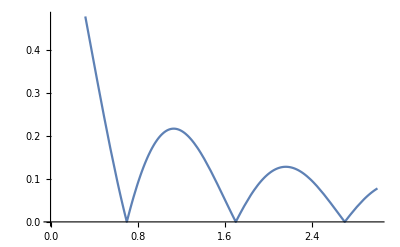

```mathematica
Φb=0.3; (*Make the magnetization less than a flux quantum, for now*)
Φ0=1; (*Normalize in terms of flux quantum*)
Ic[Φ_,bflux_]=Abs[Sin[π (Φ+bflux)/Φ0]/(π(Φ+bflux)/Φ0)]
Plot[Ic[Φ,Φb],{Φ,0,3}]
```

```mathematica
Manipulate[Plot[Ic[Φ,x],{Φ,-3,3}],{{x,0},-0.5,0.5}]
```

Changing x changes the value of the barrier flux, changing offset in fraunhofer pattern

```mathematica
Ma
```

Ma